```mathematica
soln=Solve[{-2(1-L)+2 lambda Cos[theta]+mu Sin[theta]==0,
(1/2) theta-2 lambda L Sin[theta]+mu L Cos[theta]==0},{lambda, mu}]
```

{{lambda→-(-4 L Cos[theta]+4 L^2 Cos[theta]-theta Sin[theta])/(4 L (Cos[theta]^2+Sin[theta]^2)),mu→-(theta Cos[theta]-4 L Sin[theta]+4 L^2 Sin[theta])/(2 L (Cos[theta]^2+Sin[theta]^2))}}

```mathematica
Simplify[%]
```

{{lambda→Cos[theta]-L Cos[theta]+(theta Sin[theta])/(4 L),mu→-(theta Cos[theta])/(2 L)-2 (-1+L) Sin[theta]}}

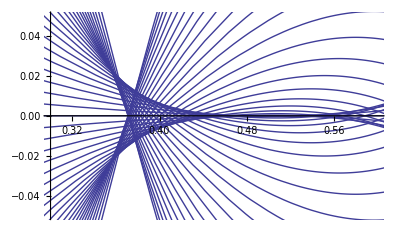

```mathematica
s=Pi/64; m=24;

Do[
	f[k_]:=ParametricPlot[{Cos[k s] - L Cos[k s] + (k s Sin[k s])/(4 L),
 		-(k s Cos[k s])/(2 L) - 2 (-1 + L) Sin[k s]}, {L, .25, 1.75},
 		PlotRange → {{.3, .6}, {-.05, .05}}],
{k,-m,m,1}];

Show[Join[Table[f[k], {k, -m, m, 1}]],AspectRatio->.6]
```